```mathematica
Clear["Global`*"];
H0=DiagonalMatrix[{-1,-1,3,-1,-1,3,-1,-1}];
V=-{{0,1,1,0,1,0,0,0},{1,0,0,1,0,1,0,0},{1,0,0,1,0,0,1,0},{0,1,1,0,0,0,0,1},{1,0,0,0,0,1,1,0},{0,1,0,0,1,0,0,1},{0,0,1,0,1,0,0,1},{0,0,0,1,0,1,1,0}};
H[hx_]:=H0+hx*V;
Hnew[hx_]:=Drop[Drop[Transpose[Drop[Drop[H[hx],{3}],{5}]],{3}],{5}];
H2[hx_]:=-hx^2/4*{{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1}};
H3Term[hx_] :=-hx^3/2/16*{{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,1,0,1,0}};
H3[hx_]:=Hnew[hx]+H2[hx]+H3Term[hx];
```

Calculate and plot approximated GS energy

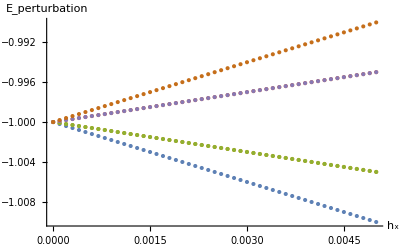

```mathematica
energynew={};
energyArraynew={};
hx=Range[0,0.005,0.0001];
Do[energynew=Append[energynew,Sort[N[Eigenvalues[H3[hx[[i]]]]],Less]],{i,Length[hx]}];
Do[AppendTo[energyArraynew,Table[{hx[[i]],energynew[[i]][[k]]},{i,1,Length[hx]}]],{k,1,Length[energynew[[1]]]}]
P1=ListPlot[energyArraynew, AxesLabel->{"h_x","E_perturbation"}]
```

Calculate and plot exact GS energies

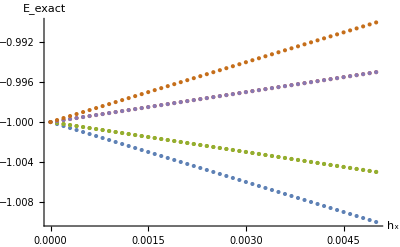

```mathematica
energy={};
energyArray={};
Do[energy=Append[energy,Sort[N[Eigenvalues[H[hx[[i]]]]],Less]],{i,Length[hx]}];
Do[AppendTo[energyArray,Table[{hx[[i]],energy[[i]][[k]]},{i,1,Length[hx]}]],{k,1,Length[energy[[1]]]}]
GSenergyArray=Drop[energyArray,-2];
P2=ListPlot[GSenergyArray, AxesLabel->{"h_x","E_exact"}]
```

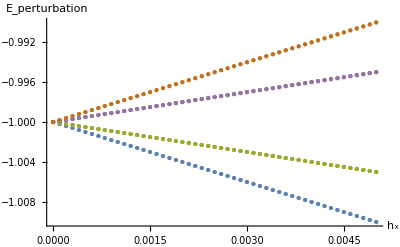

```mathematica
Show[P1,P2]
```

Calculate and plot energy errors

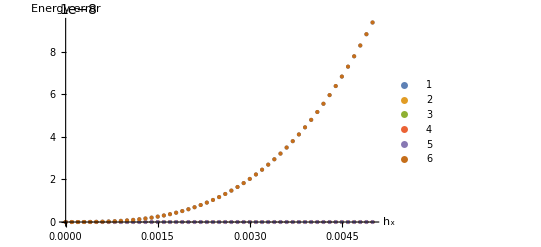

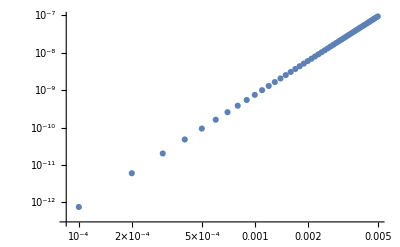

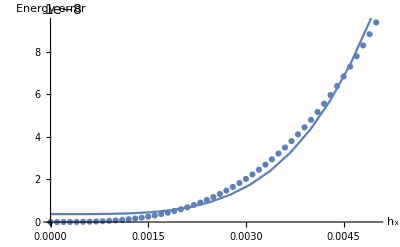

```mathematica
errorRow={};
errorArray={};
Do[
AppendTo[errorArray,Table[{hx[[j]],Abs[energyArraynew[[i]][[j]][[2]]-GSenergyArray[[i]][[j]][[2]]]},{j,Length[hx]}]],
{i,Length[energyArraynew]}]
stateIndex = 1;
cubicfit=Fit[errorArray[[stateIndex]],{1,x^4},x];
ListPlot[errorArray,PlotLegends->Automatic,PlotRange->All, AxesLabel->{"h_x", "Energy error"}]
ListLogLogPlot[errorArray[[stateIndex]],PlotLegends->Automatic,PlotRange->All]
Show[ListPlot[errorArray[[stateIndex]],PlotLegends->Automatic,PlotRange->All],Plot[cubicfit,{x,0,1}],AxesLabel->{"h_x", "Energy error"}]
```

Compare 6 probabilities; difference between exact probabilities and the approximate probabilities

Plot exact probability

```mathematica
data1={};
Do[
eigensystem=Eigensystem[H[0,hx[[x]]]];
eigenvalues=eigensystem[[1,;;]];
GSIndex=Ordering[N[eigenvalues],1];
eigenvectors=eigensystem[[2,;;]];
GSEigenvector=eigenvectors[[GSIndex]];
norm=(GSEigenvector.ConjugateTranspose[GSEigenvector])[[1]][[1]];NormedGSEigenvector=Transpose[GSEigenvector]/√norm;GSProbability=Conjugate[NormedGSEigenvector]*NormedGSEigenvector;
data1=Append[data1,N[GSProbability]],
{x,Length[hx]}];
tableArray1={};
Do[AppendTo[tableArray1,Table[{hx[[i]],data1[[i]][[k]][[1]]},{i,Length[hx]}]],{k,1,Length[data1[[1]]]}]
ExactProbabilityArray=Drop[Drop[tableArray1,{3}],{5}];
P3=ListPlot[ExactProbabilityArray,PlotLegends->Automatic,PlotRange->All]
```

Part::partw: Part 2 of Eigensystem[H[0,0.]] does not exist.

Part::partw: Part 2 of Eigensystem[H[0,0.0001]] does not exist.

Part::partw: Part 2 of Eigensystem[H[0,0.0002]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Drop::drop: Cannot drop positions 5 through 5 in {{{0.,Transpose[Eigensystem[H[0.,0.]]]/(√H[0.,0.])},{0.0001,Transpose[Eigensystem[H[0.,0.0001]]]/(√H[0.,0.0001])},«8»,«41»},{{0.,H[0.,0.]},{0.0001,H[0.,0.0001]},«8»,«41»}}.

Drop::normal: Nonatomic expression expected at position 1 in Drop[False,True].

ListPlot::lpn: Drop[{{{0.,Transpose[Eigensystem[H[«2»]]]/(√H[0.,0.])},{0.0001,Transpose[Eigensystem[H[«2»]]]/(√H[0.,0.0001])},«7»,{0.0009,Transpose[Eigensystem[H[«2»]]]/(√H[0.,0.0009])},«41»},{«1»}},{5}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[{{{0.,Transpose[Eigensystem[H[0.,0.]]]/(√H[0.,0.])},{0.0001,Transpose[Eigensystem[H[0.,0.0001]]]/(√H[0.,0.0001])},{0.0002,Transpose[Eigensystem[H[0.,0.0002]]]/(√H[0.,0.0002])},{0.0003,Transpose[Eigensystem[H[0.,0.0003]]]/(√H[0.,0.0003])},{0.0004,Transpose[Eigensystem[H[0.,0.0004]]]/(√H[0.,0.0004])},{0.0005,Transpose[Eigensystem[H[0.,0.0005]]]/(√H[0.,0.0005])},{0.0006,Transpose[Eigensystem[H[0.,0.0006]]]/(√H[0.,0.0006])},{0.0007,Transpose[Eigensystem[H[0.,0.0007]]]/(√H[0.,0.0007])},{0.0008,Transpose[Eigensystem[H[0.,0.0008]]]/(√H[0.,0.0008])},{0.0009,Transpose[Eigensystem[H[0.,0.0009]]]/(√H[0.,0.0009])},{0.001,Transpose[Eigensystem[H[0.,0.001]]]/(√H[0.,0.001])},{0.0011,Transpose[Eigensystem[H[0.,0.0011]]]/(√H[0.,0.0011])},{0.0012,Transpose[Eigensystem[H[0.,0.0012]]]/(√H[0.,0.0012])},{0.0013,Transpose[Eigensystem[H[0.,0.0013]]]/(√H[0.,0.0013])},{0.0014,Transpose[Eigensystem[H[0.,0.0014]]]/(√H[0.,0.0014])},{0.0015,Transpose[Eigensystem[H[0.,0.0015]]]/(√H[0.,0.0015])},{0.0016,Transpose[Eigensystem[H[0.,0.0016]]]/(√H[0.,0.0016])},{0.0017,Transpose[Eigensystem[H[0.,0.0017]]]/(√H[0.,0.0017])},{0.0018,Transpose[Eigensystem[H[0.,0.0018]]]/(√H[0.,0.0018])},{0.0019,Transpose[Eigensystem[H[0.,0.0019]]]/(√H[0.,0.0019])},{0.002,Transpose[Eigensystem[H[0.,0.002]]]/(√H[0.,0.002])},{0.0021,Transpose[Eigensystem[H[0.,0.0021]]]/(√H[0.,0.0021])},{0.0022,Transpose[Eigensystem[H[0.,0.0022]]]/(√H[0.,0.0022])},{0.0023,Transpose[Eigensystem[H[0.,0.0023]]]/(√H[0.,0.0023])},{0.0024,Transpose[Eigensystem[H[0.,0.0024]]]/(√H[0.,0.0024])},{0.0025,Transpose[Eigensystem[H[0.,0.0025]]]/(√H[0.,0.0025])},{0.0026,Transpose[Eigensystem[H[0.,0.0026]]]/(√H[0.,0.0026])},{0.0027,Transpose[Eigensystem[H[0.,0.0027]]]/(√H[0.,0.0027])},{0.0028,Transpose[Eigensystem[H[0.,0.0028]]]/(√H[0.,0.0028])},{0.0029,Transpose[Eigensystem[H[0.,0.0029]]]/(√H[0.,0.0029])},{0.003,Transpose[Eigensystem[H[0.,0.003]]]/(√H[0.,0.003])},{0.0031,Transpose[Eigensystem[H[0.,0.0031]]]/(√H[0.,0.0031])},{0.0032,Transpose[Eigensystem[H[0.,0.0032]]]/(√H[0.,0.0032])},{0.0033,Transpose[Eigensystem[H[0.,0.0033]]]/(√H[0.,0.0033])},{0.0034,Transpose[Eigensystem[H[0.,0.0034]]]/(√H[0.,0.0034])},{0.0035,Transpose[Eigensystem[H[0.,0.0035]]]/(√H[0.,0.0035])},{0.0036,Transpose[Eigensystem[H[0.,0.0036]]]/(√H[0.,0.0036])},{0.0037,Transpose[Eigensystem[H[0.,0.0037]]]/(√H[0.,0.0037])},{0.0038,Transpose[Eigensystem[H[0.,0.0038]]]/(√H[0.,0.0038])},{0.0039,Transpose[Eigensystem[H[0.,0.0039]]]/(√H[0.,0.0039])},{0.004,Transpose[Eigensystem[H[0.,0.004]]]/(√H[0.,0.004])},{0.0041,Transpose[Eigensystem[H[0.,0.0041]]]/(√H[0.,0.0041])},{0.0042,Transpose[Eigensystem[H[0.,0.0042]]]/(√H[0.,0.0042])},{0.0043,Transpose[Eigensystem[H[0.,0.0043]]]/(√H[0.,0.0043])},{0.0044,Transpose[Eigensystem[H[0.,0.0044]]]/(√H[0.,0.0044])},{0.0045,Transpose[Eigensystem[H[0.,0.0045]]]/(√H[0.,0.0045])},{0.0046,Transpose[Eigensystem[H[0.,0.0046]]]/(√H[0.,0.0046])},{0.0047,Transpose[Eigensystem[H[0.,0.0047]]]/(√H[0.,0.0047])},{0.0048,Transpose[Eigensystem[H[0.,0.0048]]]/(√H[0.,0.0048])},{0.0049,Transpose[Eigensystem[H[0.,0.0049]]]/(√H[0.,0.0049])},{0.005,Transpose[Eigensystem[H[0.,0.005]]]/(√H[0.,0.005])}},{{0.,H[0.,0.]},{0.0001,H[0.,0.0001]},{0.0002,H[0.,0.0002]},{0.0003,H[0.,0.0003]},{0.0004,H[0.,0.0004]},{0.0005,H[0.,0.0005]},{0.0006,H[0.,0.0006]},{0.0007,H[0.,0.0007]},{0.0008,H[0.,0.0008]},{0.0009,H[0.,0.0009]},{0.001,H[0.,0.001]},{0.0011,H[0.,0.0011]},{0.0012,H[0.,0.0012]},{0.0013,H[0.,0.0013]},{0.0014,H[0.,0.0014]},{0.0015,H[0.,0.0015]},{0.0016,H[0.,0.0016]},{0.0017,H[0.,0.0017]},{0.0018,H[0.,0.0018]},{0.0019,H[0.,0.0019]},{0.002,H[0.,0.002]},{0.0021,H[0.,0.0021]},{0.0022,H[0.,0.0022]},{0.0023,H[0.,0.0023]},{0.0024,H[0.,0.0024]},{0.0025,H[0.,0.0025]},{0.0026,H[0.,0.0026]},{0.0027,H[0.,0.0027]},{0.0028,H[0.,0.0028]},{0.0029,H[0.,0.0029]},{0.003,H[0.,0.003]},{0.0031,H[0.,0.0031]},{0.0032,H[0.,0.0032]},{0.0033,H[0.,0.0033]},{0.0034,H[0.,0.0034]},{0.0035,H[0.,0.0035]},{0.0036,H[0.,0.0036]},{0.0037,H[0.,0.0037]},{0.0038,H[0.,0.0038]},{0.0039,H[0.,0.0039]},{0.004,H[0.,0.004]},{0.0041,H[0.,0.0041]},{0.0042,H[0.,0.0042]},{0.0043,H[0.,0.0043]},{0.0044,H[0.,0.0044]},{0.0045,H[0.,0.0045]},{0.0046,H[0.,0.0046]},{0.0047,H[0.,0.0047]},{0.0048,H[0.,0.0048]},{0.0049,H[0.,0.0049]},{0.005,H[0.,0.005]}}},{5}],PlotLegends→Automatic,PlotRange→All]

Plot approximate probability

Part::partw: Part 2 of Eigensystem[H3[1,0.]] does not exist.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

Part::partd: Part specification 2.⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 2 of Eigensystem[H3[1,0.0001]] does not exist.

Part::partw: Part 2 of Eigensystem[H3[1,0.0002]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

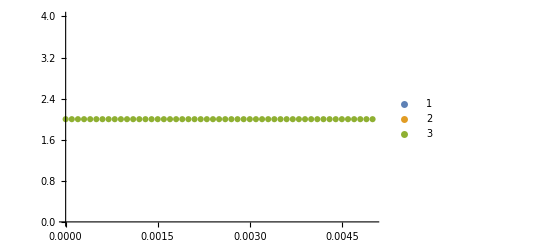

```mathematica
data2={};
Do[
eigensystem=Eigensystem[H3[1,hx[[x]]]];
eigenvalues=eigensystem[[1,;;]];
GSIndex=Ordering[N[eigenvalues],1];
eigenvectors=eigensystem[[2,;;]];
GSEigenvector=eigenvectors[[GSIndex]];
norm=(GSEigenvector.ConjugateTranspose[GSEigenvector])[[1]][[1]];NormedGSEigenvector=Transpose[GSEigenvector]/√norm;GSProbability=Conjugate[NormedGSEigenvector]*NormedGSEigenvector;
data2=Append[data2,N[GSProbability]],
{x,Length[hx]}];
tableArray2={};
Do[AppendTo[tableArray2,Table[{hx[[i]],data2[[i]][[k]][[1]]},{i,Length[hx]}]],{k,1,Length[data2[[1]]]}]
P4=ListPlot[tableArray2,PlotLegends->Automatic,PlotRange->All]
```

Compare graphs

```mathematica
Show[P3,P4]
```

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Drop[{{{0.,Power[«2»] Transpose[«1»]},{0.0001,Power[«2»] Transpose[«1»]},{0.0002,Power[«2»] Transpose[«1»]},«6»,{0.0009,Power[«2»] Transpose[«1»]},«41»},{{0.,H[0.,0.]},«10»}},{5}],«1»,«1»],].

Show[ListPlot[Drop[{{{0.,Transpose[Eigensystem[H[0.,0.]]]/(√H[0.,0.])},{0.0001,Transpose[Eigensystem[H[0.,0.0001]]]/(√H[0.,0.0001])},{0.0002,Transpose[Eigensystem[H[0.,0.0002]]]/(√H[0.,0.0002])},{0.0003,Transpose[Eigensystem[H[0.,0.0003]]]/(√H[0.,0.0003])},{0.0004,Transpose[Eigensystem[H[0.,0.0004]]]/(√H[0.,0.0004])},{0.0005,Transpose[Eigensystem[H[0.,0.0005]]]/(√H[0.,0.0005])},{0.0006,Transpose[Eigensystem[H[0.,0.0006]]]/(√H[0.,0.0006])},{0.0007,Transpose[Eigensystem[H[0.,0.0007]]]/(√H[0.,0.0007])},{0.0008,Transpose[Eigensystem[H[0.,0.0008]]]/(√H[0.,0.0008])},{0.0009,Transpose[Eigensystem[H[0.,0.0009]]]/(√H[0.,0.0009])},{0.001,Transpose[Eigensystem[H[0.,0.001]]]/(√H[0.,0.001])},{0.0011,Transpose[Eigensystem[H[0.,0.0011]]]/(√H[0.,0.0011])},{0.0012,Transpose[Eigensystem[H[0.,0.0012]]]/(√H[0.,0.0012])},{0.0013,Transpose[Eigensystem[H[0.,0.0013]]]/(√H[0.,0.0013])},{0.0014,Transpose[Eigensystem[H[0.,0.0014]]]/(√H[0.,0.0014])},{0.0015,Transpose[Eigensystem[H[0.,0.0015]]]/(√H[0.,0.0015])},{0.0016,Transpose[Eigensystem[H[0.,0.0016]]]/(√H[0.,0.0016])},{0.0017,Transpose[Eigensystem[H[0.,0.0017]]]/(√H[0.,0.0017])},{0.0018,Transpose[Eigensystem[H[0.,0.0018]]]/(√H[0.,0.0018])},{0.0019,Transpose[Eigensystem[H[0.,0.0019]]]/(√H[0.,0.0019])},{0.002,Transpose[Eigensystem[H[0.,0.002]]]/(√H[0.,0.002])},{0.0021,Transpose[Eigensystem[H[0.,0.0021]]]/(√H[0.,0.0021])},{0.0022,Transpose[Eigensystem[H[0.,0.0022]]]/(√H[0.,0.0022])},{0.0023,Transpose[Eigensystem[H[0.,0.0023]]]/(√H[0.,0.0023])},{0.0024,Transpose[Eigensystem[H[0.,0.0024]]]/(√H[0.,0.0024])},{0.0025,Transpose[Eigensystem[H[0.,0.0025]]]/(√H[0.,0.0025])},{0.0026,Transpose[Eigensystem[H[0.,0.0026]]]/(√H[0.,0.0026])},{0.0027,Transpose[Eigensystem[H[0.,0.0027]]]/(√H[0.,0.0027])},{0.0028,Transpose[Eigensystem[H[0.,0.0028]]]/(√H[0.,0.0028])},{0.0029,Transpose[Eigensystem[H[0.,0.0029]]]/(√H[0.,0.0029])},{0.003,Transpose[Eigensystem[H[0.,0.003]]]/(√H[0.,0.003])},{0.0031,Transpose[Eigensystem[H[0.,0.0031]]]/(√H[0.,0.0031])},{0.0032,Transpose[Eigensystem[H[0.,0.0032]]]/(√H[0.,0.0032])},{0.0033,Transpose[Eigensystem[H[0.,0.0033]]]/(√H[0.,0.0033])},{0.0034,Transpose[Eigensystem[H[0.,0.0034]]]/(√H[0.,0.0034])},{0.0035,Transpose[Eigensystem[H[0.,0.0035]]]/(√H[0.,0.0035])},{0.0036,Transpose[Eigensystem[H[0.,0.0036]]]/(√H[0.,0.0036])},{0.0037,Transpose[Eigensystem[H[0.,0.0037]]]/(√H[0.,0.0037])},{0.0038,Transpose[Eigensystem[H[0.,0.0038]]]/(√H[0.,0.0038])},{0.0039,Transpose[Eigensystem[H[0.,0.0039]]]/(√H[0.,0.0039])},{0.004,Transpose[Eigensystem[H[0.,0.004]]]/(√H[0.,0.004])},{0.0041,Transpose[Eigensystem[H[0.,0.0041]]]/(√H[0.,0.0041])},{0.0042,Transpose[Eigensystem[H[0.,0.0042]]]/(√H[0.,0.0042])},{0.0043,Transpose[Eigensystem[H[0.,0.0043]]]/(√H[0.,0.0043])},{0.0044,Transpose[Eigensystem[H[0.,0.0044]]]/(√H[0.,0.0044])},{0.0045,Transpose[Eigensystem[H[0.,0.0045]]]/(√H[0.,0.0045])},{0.0046,Transpose[Eigensystem[H[0.,0.0046]]]/(√H[0.,0.0046])},{0.0047,Transpose[Eigensystem[H[0.,0.0047]]]/(√H[0.,0.0047])},{0.0048,Transpose[Eigensystem[H[0.,0.0048]]]/(√H[0.,0.0048])},{0.0049,Transpose[Eigensystem[H[0.,0.0049]]]/(√H[0.,0.0049])},{0.005,Transpose[Eigensystem[H[0.,0.005]]]/(√H[0.,0.005])}},{{0.,H[0.,0.]},{0.0001,H[0.,0.0001]},{0.0002,H[0.,0.0002]},{0.0003,H[0.,0.0003]},{0.0004,H[0.,0.0004]},{0.0005,H[0.,0.0005]},{0.0006,H[0.,0.0006]},{0.0007,H[0.,0.0007]},{0.0008,H[0.,0.0008]},{0.0009,H[0.,0.0009]},{0.001,H[0.,0.001]},{0.0011,H[0.,0.0011]},{0.0012,H[0.,0.0012]},{0.0013,H[0.,0.0013]},{0.0014,H[0.,0.0014]},{0.0015,H[0.,0.0015]},{0.0016,H[0.,0.0016]},{0.0017,H[0.,0.0017]},{0.0018,H[0.,0.0018]},{0.0019,H[0.,0.0019]},{0.002,H[0.,0.002]},{0.0021,H[0.,0.0021]},{0.0022,H[0.,0.0022]},{0.0023,H[0.,0.0023]},{0.0024,H[0.,0.0024]},{0.0025,H[0.,0.0025]},{0.0026,H[0.,0.0026]},{0.0027,H[0.,0.0027]},{0.0028,H[0.,0.0028]},{0.0029,H[0.,0.0029]},{0.003,H[0.,0.003]},{0.0031,H[0.,0.0031]},{0.0032,H[0.,0.0032]},{0.0033,H[0.,0.0033]},{0.0034,H[0.,0.0034]},{0.0035,H[0.,0.0035]},{0.0036,H[0.,0.0036]},{0.0037,H[0.,0.0037]},{0.0038,H[0.,0.0038]},{0.0039,H[0.,0.0039]},{0.004,H[0.,0.004]},{0.0041,H[0.,0.0041]},{0.0042,H[0.,0.0042]},{0.0043,H[0.,0.0043]},{0.0044,H[0.,0.0044]},{0.0045,H[0.,0.0045]},{0.0046,H[0.,0.0046]},{0.0047,H[0.,0.0047]},{0.0048,H[0.,0.0048]},{0.0049,H[0.,0.0049]},{0.005,H[0.,0.005]}}},{5}],PlotLegends→Automatic,PlotRange→All],-Graphics-]

Calculate and plot probability errors

Part::partw: Part 3 of {{{0.,Transpose[Eigensystem[H[0.,0.]]]/(√H[0.,0.])},{0.0001,Transpose[Eigensystem[H[0.,0.0001]]]/(√H[0.,0.0001])},«8»,«41»},{{0.,H[0.,0.]},{0.0001,H[0.,0.0001]},«8»,«41»}} does not exist.

Part::partw: Part 4 of {{{0.,Transpose[Eigensystem[H[0.,0.]]]/(√H[0.,0.])},{0.0001,Transpose[Eigensystem[H[0.,0.0001]]]/(√H[0.,0.0001])},«8»,«41»},{{0.,H[0.,0.]},{0.0001,H[0.,0.0001]},«8»,«41»}} does not exist.

Part::partw: Part 5 of {{{0.,Transpose[Eigensystem[H[0.,0.]]]/(√H[0.,0.])},{0.0001,Transpose[Eigensystem[H[0.,0.0001]]]/(√H[0.,0.0001])},«8»,«41»},{{0.,H[0.,0.]},{0.0001,H[0.,0.0001]},«8»,«41»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 5⟦2⟧ is longer than depth of object.

Part::partd: Part specification 3⟦2⟧ is longer than depth of object.

Fit::fitd: First argument {{0.,{Abs[-0.0001+Transpose[2.]/(√Part[«2»])],Abs[Transpose[2.]/(√Part[«2»])-Transpose[Eigensystem[«1»]]/(√H[«2»])]}},«9»,«41»} in Fit is not a list or a rectangular array.

Part::partd: Part specification 5.⟦2⟧ is longer than depth of object.

Part::partd: Part specification 3.⟦2⟧ is longer than depth of object.

Part::partd: Part specification 5.⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

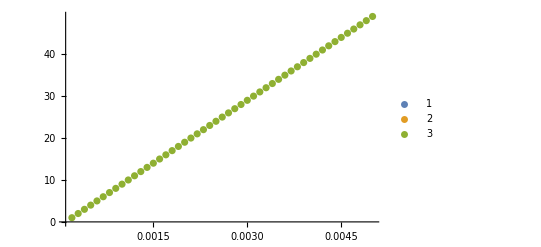

-Graphics-

General::ivar: 0.0000204286 is not a valid variable.

General::ivar: 0.0204286 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
ProbabilityErrorArray={};
Do[
AppendTo[ProbabilityErrorArray,Table[{hx[[j]],Abs[tableArray2[[i]][[j]][[2]]-ExactProbabilityArray[[i]][[j]][[2]]]},{j,Length[hx]}]],
{i,Length[tableArray2]}]
quadraticfit=Fit[ProbabilityErrorArray[[1]],{1,x^2},x];
ListPlot[ProbabilityErrorArray,PlotLegends->Automatic,PlotRange->All]
ListLogLogPlot[ProbabilityErrorArray[[1]],PlotLegends->Automatic,PlotRange->All]
Show[ListPlot[ProbabilityErrorArray[[1]],PlotLegends->Automatic,PlotRange->All],Plot[quadraticfit,{x,0,1}]]
```